This notebook is comprised of my work and I understand the content.—Shixuan Shan

# Tight Binding Model

## Shixuan Shan

Codes

## 1D Free electron energy dispersion relation

```mathematica
freeElectronE1D[shift_]:=Table[(k-(2 n)  Pi shift)^2,{n,-2,2}](*Giving a set of E(k) with different symmetry axes*)
```

```mathematica
Manipulate[Show[Table[Plot[freeElectronE1D[shift][[m]],{k,(-2 m+5) Pi+2 Pi (m-3) shift,(-2 m+7) Pi+2 Pi (m-3) shift},(*plotting the parabolas and only show each of them in specific regions*)
PlotRange->{{-brillouinZone,brillouinZone},{0,200}},
GridLines-> {Table[n Pi,{n,-4,4}],{}},GridLinesStyle->Directive[Gray, Dashed],Ticks->{Table[n Pi,{n,-4,4}],{}},(*showing Brillouin zones*)
AxesLabel->{Style["ka",14,Italic,Bold],Style["E(k)",14,Italic,Bold]},
AxesStyle-> Directive[12],
AspectRatio->1],{m,1,5}]],
{{shift,0,Style["Folding",14]},0, 1},
{{brillouinZone,5 Pi+1,Style["Brillouin Zone",14]},{5 Pi+1-> "Extended",Pi+1-> "Reduced"},Setter}]
```

## Bravais lattice (BL) and reciprocal lattice (RL)

#### The function of plotting a given BL

```mathematica
latticeGraphics[latticeType_]:=Graphics3D[{{Cyan,Opacity[1/5],Cuboid[{0,0,0},{1,1,1}]},Sphere[Flatten[Table[{latticeType[[1]] l+latticeType[[2]] m+latticeType[[3]] n},{l,-1,2},{m,-1,2},{n,-1,2}],3],1/10]},(*Giving a set of lattice points that are going to be plotted*)
PlotRange->{{-1/10,11/10},{-1/10,11/10},{-1/10,11/10}}(*Only showing the points that are in a cubic*),
Boxed->False,ImageSize->Medium]
```

#### The relationship between BL basis and RL basis

```mathematica
reciprocalLatticeBasis[latticeBasis_]:=2 Pi {Cross[latticeBasis[[2]],latticeBasis[[3]]]/(latticeBasis[[1]].Cross[latticeBasis[[2]],latticeBasis[[3]]]),Cross[latticeBasis[[3]],latticeBasis[[1]]]/(latticeBasis[[1]].Cross[latticeBasis[[2]],latticeBasis[[3]]]),Cross[latticeBasis[[1]],latticeBasis[[2]]]/(latticeBasis[[1]].Cross[latticeBasis[[2]],latticeBasis[[3]]])}(*get the three vectors of the RL basis*)
```

#### The function for calculating the mid-points of the origin and its nearest neighbors in RL and the surfaces of the first Brillouin zone (BZ)

```mathematica
nearestNeighborsAndSurfaces[crystalStructure_]:=Module[{coordinates,nearestDistance,nearestDistanceMidPoints,intercept},
(*Giving a set of points in RL*)
coordinates=Flatten[Table[q crystalStructure[[1]]+r crystalStructure[[2]]+s crystalStructure[[3]],{q,-3,3},{r,-3,3},{s,-3,3}],2];
(*Finding the nearext neighbors of the origin except the origin itself*)
nearestDistance=RankedMin[Flatten[Table[coordinates[[m,1]]^2+coordinates[[m,2]]^2+coordinates[[m,3]]^2,{m,1,Length[coordinates]}]],2];
(*Finding the mid-points of the origin and its nearest neighbors*)
nearestDistanceMidPoints=Select[coordinates,#[[1]]^2+#[[2]]^2+#[[3]]^2== nearestDistance&]*1/2 ;
(*Calculating the intercepts of the first BZ surfaces*)
intercept=Table[nearestDistanceMidPoints[[n,1]]^2+nearestDistanceMidPoints[[n,2]]^2+nearestDistanceMidPoints[[n,3]]^2,{n,1,Length[nearestDistanceMidPoints]}];
(*Printing the midpoints and the function of first BZ surfaces*)
MatrixForm[{nearestDistanceMidPoints,Table[nearestDistanceMidPoints[[n,1]]*x+nearestDistanceMidPoints[[n,2]]*y+nearestDistanceMidPoints[[n,3]]*z< nearestDistanceMidPoints[[n,1]]^2+nearestDistanceMidPoints[[n,2]]^2+nearestDistanceMidPoints[[n,3]]^2,{n,1,Length[nearestDistanceMidPoints]}]}]]
```

### SC lattice

```mathematica
simpleCubicBasis={{1,0,0},{0,1,0},{0,0,1}}
```

```mathematica
simpleCubicReciprocalLatticeBasis=reciprocalLatticeBasis[simpleCubicBasis]
```

```mathematica
nearestNeighborsAndSurfaces[simpleCubicReciprocalLatticeBasis]
```

```mathematica
scRegion=Abs[x]≤  Pi&&Abs[y]≤  Pi&&Abs[z]≤Pi
```

#### The first BZ of SC RL

```mathematica
scBZone=RegionPlot3D[scRegion,{x,-4,4},{y,-4,4},{z,-4,4},PlotPoints->60,MaxRecursion->0,Mesh-> None,PlotStyle->Directive[Yellow,Opacity[3/10]],Boxed->False,Axes->False,ImageSize->Medium]
```

### FCC lattice

```mathematica
faceCenteredCubicBasis={{0,1/2,1/2},{1/2 ,0,1/2 },{1/2 ,1/2 ,0}}
```

```mathematica
faceCenteredReciprocalLatticeBasis=reciprocalLatticeBasis[faceCenteredCubicBasis]
```

```mathematica
nearestNeighborsAndSurfaces[faceCenteredReciprocalLatticeBasis]
```

#### The first BZ of FCC RL

```mathematica
fccRegion=Abs[x]+Abs[y]+Abs[z]≤ 3 Pi
```

```mathematica
fccBZone=RegionPlot3D[fccRegion,{x,-2Pi,2Pi},{y,-2Pi,2Pi},{z,-2Pi,2Pi},Mesh-> None,PlotPoints->60,MaxRecursion->0,BoundaryStyle->None,PlotStyle->Directive[Yellow,Opacity[3/10]],Boxed->False,Axes->False,ImageSize->Medium]
```

### BCClattice

```mathematica
bodyCenteredCubicBasis={{-1/2 ,1/2 ,1/2 },{1/2 ,-1/2 ,1/2},{1/2 ,1/2 ,-1/2 }}
```

```mathematica
bodyCenteredReciprocalLatticeBasis=reciprocalLatticeBasis[bodyCenteredCubicBasis]
```

```mathematica
nearestNeighborsAndSurfaces[bodyCenteredReciprocalLatticeBasis]
```

#### The first BZ of BCC RL

```mathematica
bccRegion=Abs[x]+Abs[y]≤ 2 Pi&&Abs[y]+Abs[z]≤ 2 Pi&&Abs[x]+Abs[z]≤ 2 Pi
```

```mathematica
bccBZone=RegionPlot3D[bccRegion,{x,-2Pi,2Pi},{y,-2Pi,2Pi},{z,-2Pi,2Pi},PlotPoints->60,PlotStyle->Directive[Yellow,Opacity[3/10]],Mesh-> None,MaxRecursion->0,Boxed->False,Axes->False,ImageSize->Medium]
```

### Illustration of crystal structures

```mathematica
Manipulate[latticeGraphics[bravaisLattice],
{{bravaisLattice,simpleCubicBasis,Style["Bravais lattice",14]},{simpleCubicBasis-> " Simple cubic ",bodyCenteredCubicBasis-> " Body-centered cubic ",faceCenteredCubicBasis-> " Face-centered cubic "},Setter}]
```

## Dispersion relation of 1D atom chain by using tight binding (TB) model

### Illustration of the first two bands 1D atom chain in first BZ

```mathematica
Plot[{1−Cos[x],8+2(-1+Cos[x])},{x,-Pi,Pi},
GridLines-> {{-Pi,Pi},{}},GridLinesStyle->Directive[Gray, Dashed],Ticks->{{-Pi,Pi},{}},(*showing the Brillouin zone*)
AxesLabel->{Style["ka",14,Italic,Bold],Style["E(k)",14,Italic,Bold]},
AxesStyle-> Directive[12],
AspectRatio->1]
```

### the first two bands of a free electron

```mathematica
Plot[{x^2,(x+  2Pi )^2,(x-  2Pi )^2},{x,-Pi,Pi},GridLines-> {{-Pi,Pi},{}},
GridLinesStyle->Directive[Gray, Dashed],Ticks->{{-Pi,Pi},{}},
PlotRange->{{-Pi,Pi},{0,4 Pi^2}},
PlotStyle->{Blue,Orange,Orange},
AxesLabel->{Style["ka",14,Italic,Bold],Style["E(k)",14,Italic,Bold]},
AxesStyle-> Directive[12],
AspectRatio->1]
```

## Dispersion relation of 3D lattice by TB model

#### The simplified energy dispersion relation function for a given crystal structure

```mathematica
energyDispersion[crystalStructure_]:=Simplify[ExpToTrig[
Sum[-Exp[-2 I {kx,ky,kz}.nearestNeighborsAndSurfaces[crystalStructure][[1,1,n]]](*sum up the *),
{n,1,Length[nearestNeighborsAndSurfaces[crystalStructure][[1,1]]]}]]]
```

### SC crystal

```mathematica
energyDispersionSC=energyDispersion[simpleCubicBasis]
```

#### Plot of equal-energy surface in the first BZ for a given E

```mathematica
Manipulate[
Show[scBZone,
ContourPlot3D[energyDispersionSC==2 n ,{kx,-Pi,Pi},{ky,-Pi,Pi},{kz,-Pi,Pi},Mesh-> None,RegionFunction->Function[{x,y,z},scRegion],PlotPoints->30,MaxRecursion->0]],
{{n,-2,Style["E(k)",Italic,14]},-2,2}]
```

### FCC crystal

```mathematica
energyDispersionFCC=energyDispersion[faceCenteredCubicBasis]
```

```mathematica
Manipulate[
Show[fccBZone,
ContourPlot3D[energyDispersionFCC==2 n ,{kx,-2Pi,2Pi},{ky,-2Pi,2Pi},{kz,-2Pi,2Pi},Mesh-> None,PlotPoints->25,MaxRecursion->0,RegionFunction->Function[{x,y,z},fccRegion]]],
{{n,-2,Style["E(k)",Italic,14]},-2,2},
SaveDefinitions->True]
```

### BCC crystal

```mathematica
energyDispersionBCC=energyDispersion[bodyCenteredCubicBasis]
```

```mathematica
Manipulate[
Show[bccBZone,
ContourPlot3D[energyDispersionBCC==2 n ,{kx,-2Pi,2Pi},{ky,-2Pi,2Pi},{kz,-2Pi,2Pi},Mesh-> None,PlotPoints->25,MaxRecursion->0,RegionFunction->Function[{x,y,z},bccRegion]]],
{{n,-2,Style["E(k)",Italic,14]},-2,2},SaveDefinitions->True]
```

## An integration of the figures above in one “Manipulate”

### A list that contains the information of first BZ figures, dispersion relations and functions of first BZ surfaces for each lattice

```mathematica
dispersionPlot[x_,y_,z_]={{scBZone,energyDispersionSC,scRegion},{bccBZone,energyDispersionBCC,bccRegion},{fccBZone,energyDispersionFCC,fccRegion}};(*a function that sum up the results we get above,for example,"scBZone" is the graph of SC Brillouin zone,"energyDispersionSC" is the dispersion function of a SC reciprocal lattice,"scRegion" is the function of SC Brillouin zone*)
```

```mathematica
Manipulate[
Row[{latticeGraphics[bravaisLattice],
Show[dispersionPlot[x,y,z][[t,1]],
ContourPlot3D[dispersionPlot[x,y,z][[t,2]]==2 n ,{kx,-2 Pi,2 Pi},{ky,-2 Pi,2 Pi},{kz,-2 Pi,2 Pi},Mesh-> None,PlotPoints->30,MaxRecursion->0,RegionFunction->Function[{x,y,z},dispersionPlot[x,y,z][[t,3]]],PerformanceGoal->"Speed"]]}],
Style["Real space",16],
{{bravaisLattice,simpleCubicBasis,Style["Bravais lattice",14]},{simpleCubicBasis-> " Simple cubic ",bodyCenteredCubicBasis-> " Body-centered cubic ",faceCenteredCubicBasis-> " Face-centered cubic "},Setter,ControlPlacement->Top},
Delimiter,Style["Reciprocal space",16],
{{t,1,Style["The first Brillouin zone of",14]},{1-> " Simple cubic ",2-> " Body-centered cubic ",3-> " Face-centered cubic "},Setter},
{{n,-2,Style["E(k)",Italic,14]},-2,2}]
```

Presentation

## Free Electron

### Hamiltonian

H=P^2/(2m)

### Wave function

ψ=C ⅇ^(i k x)

### Energy dispersion relation

E(k)=(ℏ^2 k^2)/(2m)

## Overlapping of Wave Functions

-Graphics-

(a) the wave function when the atoms are far away from each other

-Graphics-

bonding orbital                                                                              antibonding orbital
(b) the wave function when the atoms are close

## Tight Binding Model

### The atomic potential of a single atom: U(r)

[P^2/(2m)+U(r)]ϕ(r)=E_0 ϕ(r)

### Taking the influence of other atoms into account:

ψ_k(r )=∑ _j a_j ϕ(r-r_j)=1/(√N)∑ _j ⅇ^(i k·r_j)ϕ(r-r_j)

### First order correction of the energy:

⟨k|H|k⟩=1/N∑ _j ∑ _m ⅇ^(i k·(r_j-r_m))∫ϕ^⋆(r-r_m)H ϕ(r-r_j) dr

### Only consider the influence of the nearest neighbors:

⟨k|H|k⟩=∑ _n ⅇ^(-i k·ρ_n)∫ϕ^⋆(r-ρ_n)H ϕ(r) dr               ( ρ_n=r_m-r_j )

### Let J_0=-∫ϕ^⋆(r)H ϕ(r) dr and J_n=-∫ϕ^⋆(r-ρ_n)H ϕ(r) dr

E(k)=E_0-J_0- ∑ _n J_n ⅇ^(-i k·ρ_n)

## What has changed?

E(k)=E_0-J_0- ∑ _n J_n ⅇ^(-i k·ρ_n)

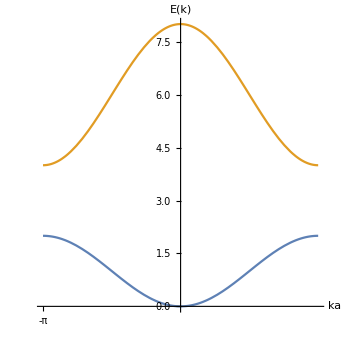
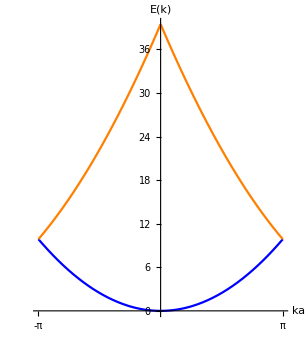

(a) TB model result                                                                              (b) free electron

## In a 3D crystal

### The relationship between primitive vectors and reciprocal primitive vectors

#### -Graphics-

### Simple cubic

E(k)=E_0-J_0-2 J (cos(k_x a)+cos(k_y a)+cos(k_z a))

### Body-centered cubic

E(k)=E_0-J_0-8 J cos((k_x a)/2) cos((k_y a)/2)cos((k_z a)/2)

### Face-centered cubic

E(k)=E_0-J_0-4J [cos((k_x a)/2) cos((k_y a)/2)+cos((k_y a)/2) cos((k_z a)/2)+cos((k_x a)/2)cos((k_z a)/2)]

## What does it look like?

Part::partd: Part specification dispersionPlot[x,y,z]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification dispersionPlot[x,y,z]⟦1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[dispersionPlot[x,y,z]⟦1,1⟧,ContourPlot3D[dispersionPlot[x,y,z]⟦FE`t$$109,2⟧==2 FE`n$$109,{kx,-2 π,2 π},{ky,-2 π,2 π},«4»,RegionFunction→Function[{x$,y$,z$},dispersionPlot[x$,y$,z$]⟦FE`t$$109,3⟧],PerformanceGoal→Speed]].